## Introduction

The document investigates time ordering photon codes and their performance

## Assumptions and function definitions

```mathematica
nb=NotebookOpen["W:\\Projects\\Dbdoctor\\Dbdoctor.PhD\\Dbdoctor.PhD.Common\\Mathematica\\QFunc.nb"];
NotebookEvaluate[nb,InsertResults->False];
```

#### SeqA010672

Calculates the sequence A010672 in oeis.org

```mathematica
SeqA010672[n_]:=Module[{cands,A},
cands=Table[ii,{ii,1,n}];
A={};
While[Length[cands]>1,
AppendTo[A,Min[cands]];
];
Print[A];
]
```

```mathematica
PErr
```

```mathematica
SimpleSeq={1,2,3,4};(*average photon number =n/2*)
```

```mathematica
HH0H00V000 (*1,2,3,4     N=10, average photons per block = 4, Average number of photns per time bin n/N=0.4*)
```

```mathematica
(*Compare with PPM, all blocks are the same length*)
```

```mathematica
SeqA010672[n_]:=Module[{cands,A},
A={1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475,530,545,607,716,797,861,964,1059,1160,1306,1385,1434,1555,1721,1833,1933,2057,2260,2496,2698,2873,3060,3196,3331,3628,3711,3867,4139,4446,4639};
Print[A[[1;;n]]];
]
```

#### Perr

Calculates the probability for any combination of l loss errors and a add errors

```mathematica
Perr[l_,a_,n_,N_, pl_, pa_]:=Module[{},
Binomial[n,l]pl^l (1-pl)^(n-l)Binomial[N-n,a]pa^a(1-pa)^(N-n-a)
]
```

```mathematica
Perr[1,0,3,7,p1,p2]
```

3 (1-p1)^2 p1 (1-p2)^4

```mathematica
HH0V000 (*n=3, N=7*)
(**)
```

```mathematica
PSuccess=Perr[0,0,3,7,p,p]+Perr[1,0,3,7,p,p]+Perr[0,1,3,7,p,p];
PSuccess2=Perr[0,0,3,7,p,p]+Perr[1,0,3,7,p,p]+Perr[0,1,3,7,p,p]+Perr[1,1,3,7,p,p]+Perr[0,2,3,7,p,p]+Perr[2,0,3,7,p,p];
PDetect=1-PSuccess
```

1-(1-p)^7-7 (1-p)^6 p

There is a a probability to correct SOME 2 errors also. We cannot correct the ADJACENT 2-errors but all other 2-errors.

1-(1-p)^7-7 (1-p)^6 p

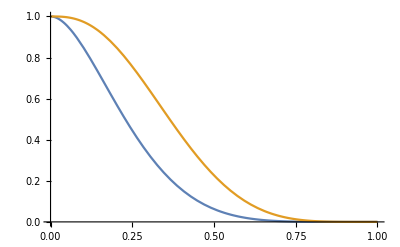

```mathematica
Plot[{PSuccess,PSuccess2}, {p,0,1}]
```

```mathematica
PSuccess1=Perr[0,0,3,7,p1,p2]+Perr[1,0,3,7,p1,p2]+Perr[0,1,3,7,p1,p2];
PSuccess2=Perr[0,0,3,7,p1,p2]+Perr[1,0,3,7,p1,p2]+Perr[0,1,3,7,p1,p2]+Perr[1,1,3,7,p1,p2]+Perr[0,2,3,7,p1,p2]+Perr[2,0,3,7,p1,p2];
```

```mathematica
Plot3D[{PSuccess1,PSuccess2}, {p1,0,1},{p2,0,1}]
```

-Graphics3D-

```mathematica
SeqA010672[20]
```

{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}

```mathematica
ListPlot[SeqA010672[20]]
```

{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

```mathematica
ListPlot[Null]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

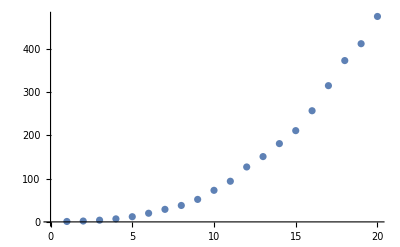

```mathematica
ListPlot[{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}]
```

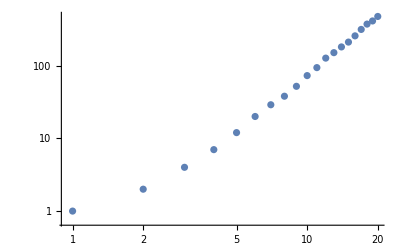

```mathematica
ListLogLogPlot[{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}]
```

```mathematica
Table[Binomial[ii,2],{ii,1,6}]
```

{0,1,3,6,10,15}

```mathematica
Binomial[14,4]//N
```

1001.

## Reference code, distance 3

#### ErrorOps

Returns all m-lists with n elements taken from ESet and all other elements are defop (default operator).
Example: ErrorOps[5,1,{xx,yy,zz},uno] gives 15 elements: {{uno,uno,uno,uno,xx},{uno,uno,uno,xx,uno},{uno,uno,xx,uno,uno},...

```mathematica
ErrorOps[m_,n_,ESet_,defop_]:=Module[{nEset,mEset,Defset,mask,temp,vect},
nEset=Tuples[ESet,{n}];
mEset={};
Defset=ConstantArray[defop,m-n];
(*mask is a list of positions where a default operator should be inserted*)
mask=DeleteDuplicates[Sort[#]&/@Permutations[Range[m],{m-n}]];(*Since it is sorted, we can insert into these positions later*)
Do[
Do[
temp=nEset[[ii]];
Do[
temp=Insert[temp,defop,kk];
,{kk,mask[[jj]]}
];
AppendTo[mEset,temp];
,{jj,Length[mask]}
];

,{ii,1,Length[nEset]}
];
mEset//DeleteDuplicates
]
```

#### CreateAllTransitions

Given a list of words , calculate what words result in each other, i.e., {1,0}->{0,0} or {1,1} so if the first state has position 1 and the second 2, we get {1,2} as output

```mathematica
CreateAllTransitions[AllStates_]:=Module[{ii,jj,result,N,temp},
result={};
N=AllStates[[1]]//Length;(*Assume all states have the same length*)
Do[
Do[
temp=AllStates[[ii]];
If[MatchQ[AllStates[[ii,jj]],1],
temp[[jj]]=0;
AppendTo[result,{ii,FirstPosition[AllStates,temp][[1]]}];];
If[MatchQ[AllStates[[ii,jj]],0],
temp[[jj]]=1;
AppendTo[result,{ii,FirstPosition[AllStates,temp][[1]]}];];
,{ii,1,AllStates//Length}];
,{jj,1,N}];
result//DeleteDuplicates
]
```

### N=5

```mathematica
NN=5;
AllStates=CreateAllStates[NN,{0,1}](*We limit possible states to only 2 excited states (1)*)
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

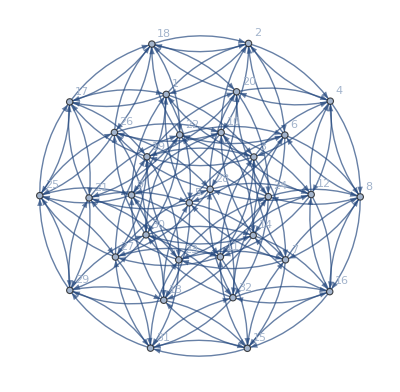

```mathematica
g=Graph[Range[NN],(#1⟦1⟧-> #1⟦2⟧&)/@CreateAllTransitions[CreateAllStates[NN,{0,1}]],VertexLabels->"Name",ImagePadding->10]
```

```mathematica
g2=GraphPower[g,2]
```

-Graphics-

```mathematica
FindIndependentVertexSet[g2]
```

{{1,20,29,16}}

```mathematica
res=FindClassicalCode[3,2]
res[[1]][[#]]&/@res[[2]][[1]]//Length
```

{{0,0,0},{0,1,1},{1,0,1},{1,1,0}}

0

```mathematica
FindClassicalCode[3,2]
```

Part::pkspec1: The expression {{1,4,6,7}} cannot be used as a part specification.

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}⟦{{1,4,6,7}}⟧

```mathematica
EL=EdgeList[g2]
VL=VertexList[g2]
```

{1->NotFound,2->NotFound,3->NotFound,4->NotFound,5->NotFound,6->NotFound,7->NotFound,8->NotFound,9->NotFound,10->NotFound}

{1,2,3,4,5,NotFound,6,7,8,9,10}

```mathematica
m=AdjacencyMatrix[g2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

#### Here is a deep-dive into how to go from the directed graph to the undirected graph

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

{{1,2,9,4,5}}

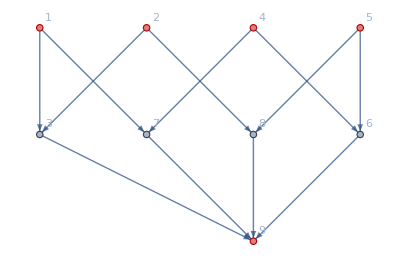

```mathematica
FindIndependentVertexSet[g]
HighlightGraph[g,%,GraphHighlightStyle->"Thick"]
```

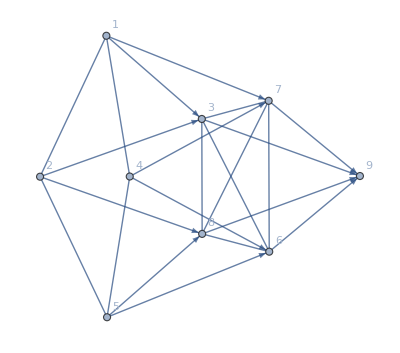

```mathematica
g2=DirectedGraphPower[g,1]
```

```mathematica
g2//EdgeList
```

{1->7,2->8,3->9,4->7,5->8,6->9,1->3,2->3,4->6,5->6,7->9,8->9,1<->4,2<->5,1<->2,7<->8,7<->3,7<->6,8<->3,8<->6,3<->6,4<->5}

Note how the new adjacency matrix is formed by connecting e.g., vertex 1 and 2 with a undirected edge, because 1 and 2 have a common final state.
Also note (I am fairly certain of this however it was more than a year that I wrote the algorithm) that FindIndependentVertexSet works irrespectively of if the edges are directed or not. Thus we could in principle make the matrix below symmetric.

Find out the codewords for correcting one error

{{1,5,9}}

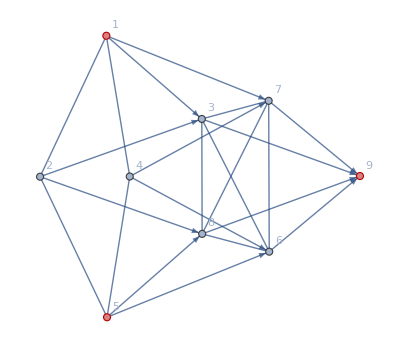

```mathematica
FindIndependentVertexSet[g2]
HighlightGraph[g2,%,GraphHighlightStyle->"Thick"]
```

Check which number belongs to which state

```mathematica
AllStates[[#]]&/@FindIndependentVertexSet[g2]
```

{{{H,H},{V,V},{0,0}}}

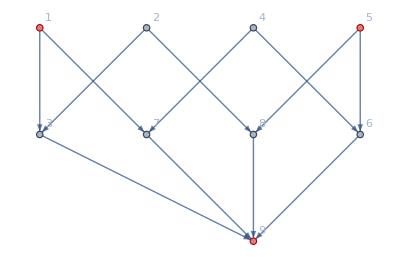

```mathematica
HighlightGraph[g,{{1,5,9}},GraphHighlightStyle->"Thick"]
```

Now a quick check to see what happens if we make all edges in g2 undirected:

```mathematica
adj2=AdjacencyMatrix[g2];
```

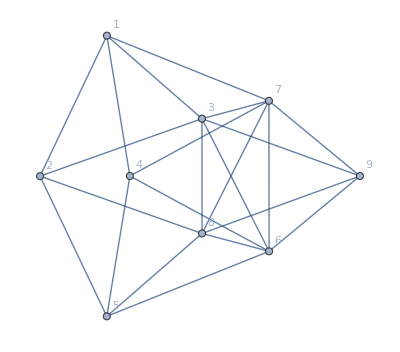
{-Graphics-,-Graphics-}

```mathematica
{g2, Undirect[g2]}
```

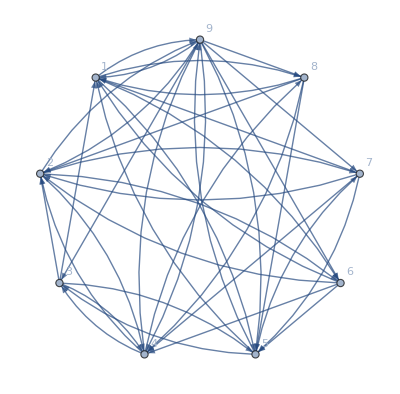
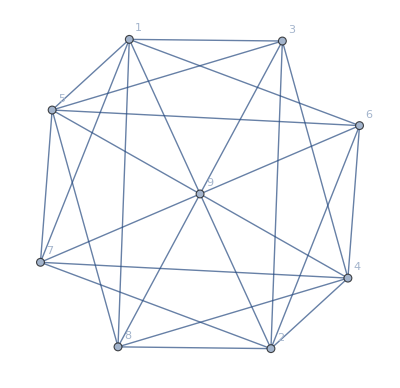

```mathematica
{GraphComplement[g2,VertexLabels->"Name"],Undirect[GraphComplement[g2,VertexLabels->"Name"]]}
```

```mathematica
{GraphComplement[g2]//EdgeList,Undirect[GraphComplement[g2]]//EdgeList}
```

{{1->5,1->6,1->8,1->9,2->4,2->6,2->7,2->9,3->1,3->2,3->4,3->5,4->2,4->3,4->8,4->9,5->1,5->3,5->7,5->9,6->1,6->2,6->4,6->5,7->1,7->2,7->4,7->5,8->1,8->2,8->4,8->5,9->1,9->2,9->3,9->4,9->5,9->6,9->7,9->8},{1<->3,1<->5,1<->6,1<->7,1<->8,1<->9,2<->3,2<->4,2<->6,2<->7,2<->8,2<->9,3<->4,3<->5,3<->9,4<->6,4<->7,4<->8,4<->9,5<->6,5<->7,5<->8,5<->9,6<->9,7<->9,8<->9}}

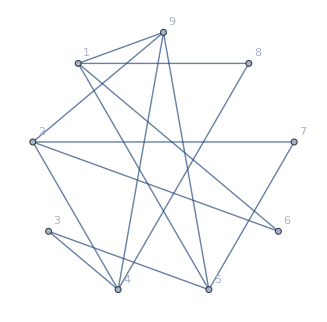
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{GraphComplement[g2,VertexLabels->"Name"],GraphComplement[Undirect[g2],VertexLabels->"Name"],Undirect[GraphComplement[g2,VertexLabels->"Name"]]}
```

```mathematica
{FindIndependentVertexSet[g2],FindIndependentVertexSet[Undirect[g2]]}
```

{{{1,5,9}},{{1,5,9}}}

```mathematica
{FindClique[GraphComplement[g2]],FindClique[GraphComplement[Undirect[g2]]],FindClique[Undirect[GraphComplement[g2]]]}
```

{{{1,5,9}},{{1,5,9}},{{1,3,5,9}}}

```mathematica
GraphComplement[Undirect[g2]]//EdgeList//Length
```

14

```mathematica
Undirect[GraphComplement[g2]]//EdgeList//Length
```

26